```mathematica
d2[n_,k_]:=d2[n,k]=Sum[d2[j,k-1] d2[n/j,1],{j,Divisors[n]}];d2[n_,1]:=d2[n,1]=1;d2[1,1]:=0;d2[n_,0]:=0;d2[1,0]:=1

d[n_,k_]:=d[n,k]=Sum[d[j,k-1] d[n/j,1],{j,Divisors[n]}];d[n_,1]:=1;d[n_,0]:=d[n,0]=0;d[1,0]:=1

K[n_,0]:=K[n,0]=If[n==1,1,0]
K[n_,1]:=K[n,1]=If[n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K[n_,k_]:=K[n,k]=Sum[K[j,k-1] K[n/j,1],{j,Divisors[n]}]
K1[n_,k_] := K1[n,k]=Sum[Binomial[k,j] K[n,k-j],{j,0,k}]

sc[f_,k_,t_] := SeriesCoefficient[Series[f[x],{x,0,Floor[t]}],k]

q2[b_,f_,n_,0]:=q2[b,f,n,0]=1
q2[b_,f_, n_,1]:= q2[b,f,n,1]=Sum[ b[n,k] sc[f,k,N[Floor[Log[2,n]]]],{k,0,N[Log[2,n]]}]
q2[b_,f_,n_,k_] := q2[b,f,n,k] = Sum[q2[b,f,n/j,k-1]q2[b,f,j,1],{j,Divisors[n]}]

q1[b_,f_,n_,0]:=q1[b,f,n,0]=1
q1[b_,f_, n_,1]:= q1[b,f,n,1]=Sum[ b[n,k] sc[f,k,20],{k,0,20}]
q1[b_,f_,n_,k_] := q1[b,f,n,k] = Sum[q1[b,f,n/j,k-1]q1[b,f,j,1],{j,Divisors[n]}]

GG[x_] := x/Log[1+x]
GG2[x_] := x/Log[1-x]
Mcos[x_] := -Cos[x]
Msin[x_] := -Sin[x]
Expd[x_] := E^x
Lg1[x_] := Log[x+1]
Lg2[x_] :=Log[1-x]
ggp[n_,k_]:= q2[K,GG,n,k]
ggp2[n_,k_]:= q2[K,GG2,n,k]
ggd2[n_,k_]:=ggd2[n,k]=q2[d2,GG2,n,k]
ggd2i[n_,k_]:=ggd2i[n,k]=q2[d2,GG,n,k]
ggdx[n_,k_]:= q2[ggd2,GG2,n,k]
ggdxi[n_,k_]:= q2[ggd2i,GG,n,k]
lg1[n_,k_]:= q2[d2,Lg1,n,k]
lg2[n_,k_]:= q2[d2,Lg2,n,k]
lg2d[n_,k_]:= q1[d,Lg2,n,k]
expd[n_,k_]:= q1[d,Expd,n,k]
expd2[n_,k_]:= q2[d2,Expd,n,k]
expk[n_,k_]:= q2[K,Expd,n,k]
sind[n_,k_]:= q1[K1,Sin,n,k]
cosd[n_,k_]:= q1[K1,Cos,n,k]
mcosd[n_,k_]:= q1[K1,Mcos,n,k]
msind[n_,k_]:= q1[K1,Msin,n,k]
tand[n_,k_]:= q2[d2,Tan,n,k]
asinsind[n_,k_]:= q2[sind,ArcSin,n,k]
atantand[n_,k_]:= q2[tand,ArcTan,n,k]

LL[f_,n_,k_] := LL[f,n,k] = Sum[ f[j,k],{j,1,n}]
```

```mathematica
Table[{n,ggp2[n,1], ggd2[n,1], ggdx[n,1]},{n,1,100}]//TableForm
```

1 | -1 | -1 | -1
2 | 1/2 | 1/2 | -3/4
3 | 1/2 | 1/2 | -3/4
4 | 1/3 | 7/12 | -113/144
5 | 1/2 | 1/2 | -5/6
6 | 1/6 | 2/3 | -53/72
7 | 1/2 | 1/2 | -5/6
8 | 7/24 | 17/24 | -25/36
9 | 1/3 | 7/12 | -107/144
10 | 1/6 | 2/3 | -103/144
11 | 1/2 | 1/2 | -37/48
12 | 5/24 | 23/24 | -43/72
13 | 1/2 | 1/2 | -37/48
14 | 1/6 | 2/3 | -103/144
15 | 1/6 | 2/3 | -103/144
16 | 209/720 | 649/720 | -303769/518400
17 | 1/2 | 1/2 | -593/720
18 | 5/24 | 23/24 | -2333/4320
19 | 1/2 | 1/2 | -593/720
20 | 5/24 | 23/24 | -2333/4320
21 | 1/6 | 2/3 | -763/1080
22 | 1/6 | 2/3 | -763/1080
23 | 1/2 | 1/2 | -593/720
24 | 103/360 | 533/360 | -35479/129600
25 | 1/3 | 7/12 | -661/864
26 | 1/6 | 2/3 | -763/1080
27 | 7/24 | 17/24 | -2981/4320
28 | 5/24 | 23/24 | -2333/4320
29 | 1/2 | 1/2 | -593/720
30 | 1/4 | 5/4 | -269/720
31 | 1/2 | 1/2 | -593/720
32 | 113/360 | 1739/1440 | -245431/518400
33 | 1/6 | 2/3 | -3187/4320
34 | 1/6 | 2/3 | -3187/4320
35 | 1/6 | 2/3 | -3187/4320
36 | 13/40 | 209/120 | -19979/86400
37 | 1/2 | 1/2 | -2237/2880
38 | 1/6 | 2/3 | -3187/4320
39 | 1/6 | 2/3 | -3187/4320
40 | 103/360 | 533/360 | -186061/518400
41 | 1/2 | 1/2 | -2237/2880
42 | 1/4 | 5/4 | -2827/5760
43 | 1/2 | 1/2 | -2237/2880
44 | 5/24 | 23/24 | -21229/34560
45 | 5/24 | 23/24 | -21229/34560
46 | 1/6 | 2/3 | -3187/4320
47 | 1/2 | 1/2 | -2237/2880
48 | 49/120 | 3503/1440 | 62441/518400
49 | 1/3 | 7/12 | -2617/3456
50 | 5/24 | 23/24 | -21229/34560
51 | 1/6 | 2/3 | -3187/4320
52 | 5/24 | 23/24 | -21229/34560
53 | 1/2 | 1/2 | -2237/2880
54 | 103/360 | 533/360 | -186061/518400
55 | 1/6 | 2/3 | -3187/4320
56 | 103/360 | 533/360 | -186061/518400
57 | 1/6 | 2/3 | -3187/4320
58 | 1/6 | 2/3 | -3187/4320
59 | 1/2 | 1/2 | -2237/2880
60 | 53/120 | 101/40 | 8743/57600
61 | 1/2 | 1/2 | -2237/2880
62 | 1/6 | 2/3 | -3187/4320
63 | 5/24 | 23/24 | -21229/34560
64 | 21821/60480 | 103133/60480 | -395646487/1828915200
65 | 1/6 | 2/3 | -2377/3456
66 | 1/4 | 5/4 | -2579/6720
67 | 1/2 | 1/2 | -8261/10080
68 | 5/24 | 23/24 | -129617/241920
69 | 1/6 | 2/3 | -2377/3456
70 | 1/4 | 5/4 | -2579/6720
71 | 1/2 | 1/2 | -8261/10080
72 | 191/360 | 2437/720 | 8827/16200
73 | 1/2 | 1/2 | -8261/10080
74 | 1/6 | 2/3 | -2377/3456
75 | 5/24 | 23/24 | -129617/241920
76 | 5/24 | 23/24 | -129617/241920
77 | 1/6 | 2/3 | -2377/3456
78 | 1/4 | 5/4 | -2579/6720
79 | 1/2 | 1/2 | -8261/10080
80 | 49/120 | 3503/1440 | 883667/7257600
81 | 209/720 | 649/720 | -22507/38400
82 | 1/6 | 2/3 | -2377/3456
83 | 1/2 | 1/2 | -8261/10080
84 | 53/120 | 101/40 | 202589/1209600
85 | 1/6 | 2/3 | -2377/3456
86 | 1/6 | 2/3 | -2377/3456
87 | 1/6 | 2/3 | -2377/3456
88 | 103/360 | 533/360 | -13501/44800
89 | 1/2 | 1/2 | -8261/10080
90 | 53/120 | 101/40 | 202589/1209600
91 | 1/6 | 2/3 | -2377/3456
92 | 5/24 | 23/24 | -129617/241920
93 | 1/6 | 2/3 | -2377/3456
94 | 1/6 | 2/3 | -2377/3456
95 | 1/6 | 2/3 | -2377/3456
96 | 6001/10080 | 10567/2520 | 281881763/304819200
97 | 1/2 | 1/2 | -8261/10080
98 | 5/24 | 23/24 | -129617/241920
99 | 5/24 | 23/24 | -129617/241920
100 | 13/40 | 209/120 | -55687/302400

```mathematica
Table[{n,N[LL[ggp2,n,1]], N[LL[ggd2,n,1]],N[LL[ ggdx,n,1]]},{n,1,100}]//TableForm
```

1 | -1. | -1. | -1.
2 | -0.5 | -0.5 | -1.75
3 | 0. | 0. | -2.5
4 | 0.333333 | 0.583333 | -3.28472
5 | 0.833333 | 1.08333 | -4.11806
6 | 1. | 1.75 | -4.85417
7 | 1.5 | 2.25 | -5.6875
8 | 1.79167 | 2.95833 | -6.38194
9 | 2.125 | 3.54167 | -7.125
10 | 2.29167 | 4.20833 | -7.84028
11 | 2.79167 | 4.70833 | -8.61111
12 | 3. | 5.66667 | -9.20833
13 | 3.5 | 6.16667 | -9.97917
14 | 3.66667 | 6.83333 | -10.6944
15 | 3.83333 | 7.5 | -11.4097
16 | 4.12361 | 8.40139 | -11.9957
17 | 4.62361 | 8.90139 | -12.8193
18 | 4.83194 | 9.85972 | -13.3594
19 | 5.33194 | 10.3597 | -14.183
20 | 5.54028 | 11.3181 | -14.723
21 | 5.70694 | 11.9847 | -15.4295
22 | 5.87361 | 12.6514 | -16.136
23 | 6.37361 | 13.1514 | -16.9596
24 | 6.65972 | 14.6319 | -17.2333
25 | 6.99306 | 15.2153 | -17.9984
26 | 7.15972 | 15.8819 | -18.7049
27 | 7.45139 | 16.5903 | -19.3949
28 | 7.65972 | 17.5486 | -19.935
29 | 8.15972 | 18.0486 | -20.7586
30 | 8.40972 | 19.2986 | -21.1322
31 | 8.90972 | 19.7986 | -21.9558
32 | 9.22361 | 21.0063 | -22.4292
33 | 9.39028 | 21.6729 | -23.167
34 | 9.55694 | 22.3396 | -23.9047
35 | 9.72361 | 23.0063 | -24.6424
36 | 10.0486 | 24.7479 | -24.8737
37 | 10.5486 | 25.2479 | -25.6504
38 | 10.7153 | 25.9146 | -26.3881
39 | 10.8819 | 26.5813 | -27.1259
40 | 11.1681 | 28.0618 | -27.4848
41 | 11.6681 | 28.5618 | -28.2615
42 | 11.9181 | 29.8118 | -28.7523
43 | 12.4181 | 30.3118 | -29.5291
44 | 12.6264 | 31.2701 | -30.1433
45 | 12.8347 | 32.2285 | -30.7576
46 | 13.0014 | 32.8951 | -31.4953
47 | 13.5014 | 33.3951 | -32.2721
48 | 13.9097 | 35.8278 | -32.1516
49 | 14.2431 | 36.4111 | -32.9088
50 | 14.4514 | 37.3694 | -33.5231
51 | 14.6181 | 38.0361 | -34.2608
52 | 14.8264 | 38.9944 | -34.8751
53 | 15.3264 | 39.4944 | -35.6518
54 | 15.6125 | 40.975 | -36.0107
55 | 15.7792 | 41.6417 | -36.7485
56 | 16.0653 | 43.1222 | -37.1074
57 | 16.2319 | 43.7889 | -37.8451
58 | 16.3986 | 44.4556 | -38.5829
59 | 16.8986 | 44.9556 | -39.3596
60 | 17.3403 | 47.4806 | -39.2078
61 | 17.8403 | 47.9806 | -39.9845
62 | 18.0069 | 48.6472 | -40.7223
63 | 18.2153 | 49.6056 | -41.3365
64 | 18.5761 | 51.3108 | -41.5529
65 | 18.7427 | 51.9775 | -42.2407
66 | 18.9927 | 53.2275 | -42.6244
67 | 19.4927 | 53.7275 | -43.444
68 | 19.7011 | 54.6858 | -43.9798
69 | 19.8677 | 55.3525 | -44.6676
70 | 20.1177 | 56.6025 | -45.0513
71 | 20.6177 | 57.1025 | -45.8709
72 | 21.1483 | 60.4872 | -45.326
73 | 21.6483 | 60.9872 | -46.1455
74 | 21.815 | 61.6539 | -46.8333
75 | 22.0233 | 62.6122 | -47.3691
76 | 22.2316 | 63.5705 | -47.9049
77 | 22.3983 | 64.2372 | -48.5927
78 | 22.6483 | 65.4872 | -48.9765
79 | 23.1483 | 65.9872 | -49.796
80 | 23.5566 | 68.4198 | -49.6743
81 | 23.8469 | 69.3212 | -50.2604
82 | 24.0136 | 69.9879 | -50.9482
83 | 24.5136 | 70.4879 | -51.7677
84 | 24.9552 | 73.0129 | -51.6002
85 | 25.1219 | 73.6795 | -52.288
86 | 25.2886 | 74.3462 | -52.9758
87 | 25.4552 | 75.0129 | -53.6636
88 | 25.7414 | 76.4934 | -53.965
89 | 26.2414 | 76.9934 | -54.7845
90 | 26.683 | 79.5184 | -54.617
91 | 26.8497 | 80.1851 | -55.3048
92 | 27.058 | 81.1434 | -55.8406
93 | 27.2247 | 81.8101 | -56.5284
94 | 27.3914 | 82.4768 | -57.2162
95 | 27.558 | 83.1434 | -57.904
96 | 28.1534 | 87.3367 | -56.9792
97 | 28.6534 | 87.8367 | -57.7987
98 | 28.8617 | 88.795 | -58.3345
99 | 29.07 | 89.7534 | -58.8703
100 | 29.395 | 91.495 | -59.0545

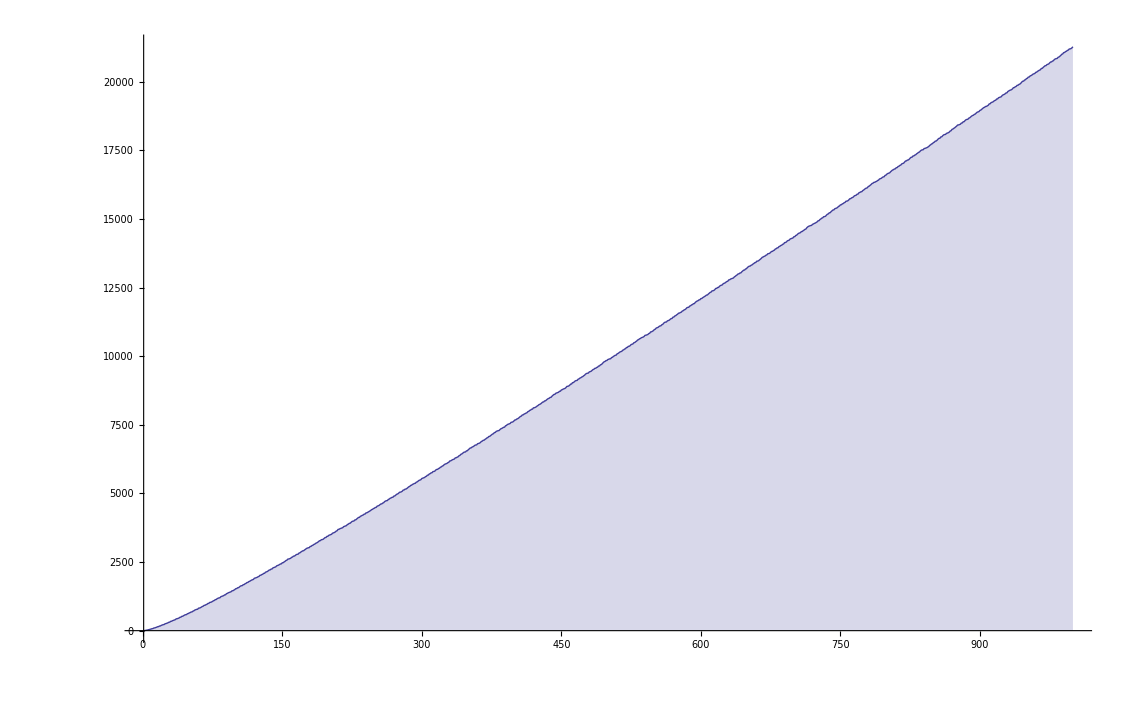

```mathematica
DiscretePlot[ LL[ ggp,n,8],{n,1,1000}]
```

```mathematica
Series[x/Log[1+x],{x,0,20}]
```

1+x/2-x^2/12+x^3/24-(19 x^4)/720+(3 x^5)/160-(863 x^6)/60480+(275 x^7)/24192-(33953 x^8)/3628800+(8183 x^9)/1036800-(3250433 x^10)/479001600+(4671 x^11)/788480-(13695779093 x^12)/2615348736000+(2224234463 x^13)/475517952000-(132282840127 x^14)/31384184832000+(2639651053 x^15)/689762304000-(111956703448001 x^16)/32011868528640000+(50188465 x^17)/15613165568-(2334028946344463 x^18)/786014494949376000+(301124035185049 x^19)/109285437800448000-(12365722323469980029 x^20)/4817145976189747200000+O[x]^21

```mathematica
Series[Log[1+x]/x,{x,0,20}]
```

1-x/2+x^2/3-x^3/4+x^4/5-x^5/6+x^6/7-x^7/8+x^8/9-x^9/10+x^10/11-x^11/12+x^12/13-x^13/14+x^14/15-x^15/16+x^16/17-x^17/18+x^18/19-x^19/20+x^20/21+O[x]^21